```mathematica
gpu=MovingAverage[Import[NotebookDirectory[]<>"4890.csv","CSV"],1];
cpu=MovingAverage[Import[NotebookDirectory[]<>"Corei7.csv","CSV"],1];
```

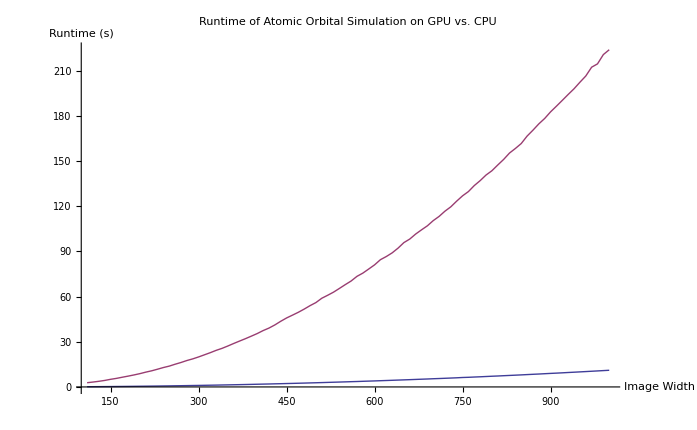

```mathematica
ListLinePlot[{gpu,cpu},PlotStyle->Thick,PlotRange->All,AxesOrigin->{100,0},AxesLabel->{"Image Width","Runtime (s)"},PlotLabel->"Runtime of Atomic Orbital Simulation on GPU vs. CPU"]
```

```mathematica
Last[Last[cpu]]
```

224.047

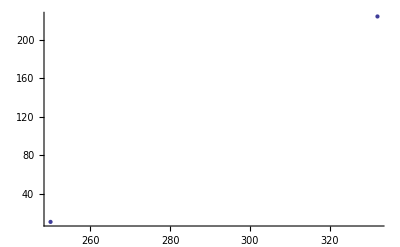

```mathematica
ListPlot[{{250,11.0755},{332,224.047}},AxesOrigin->{0,0},PlotRange->All]
```

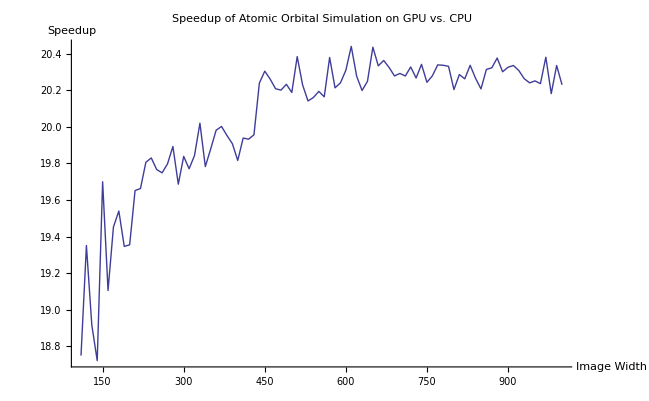

```mathematica
Speedup[a_,b_]:={a[[1]],b[[2]]/a[[2]]};
speedups=MapThread[Speedup,{gpu,cpu}];
ListLinePlot[speedups,PlotStyle->Thick,PlotRange->All,AxesOrigin->{100,18},AxesLabel->{"Image Width","Speedup"},PlotLabel->"Speedup of Atomic Orbital Simulation on GPU vs. CPU"]
```